```mathematica
ClearAll["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
(*The Following Analysis is incorrect. The reason is 2 fold. 
1. We extended the Fermi liquid phase into the region SC region in order to measure Δη which is not correct. Infact the small latent heat (atleast in comparison to the stress vs Transition temperature plot used here) that we think we get makes sense from the point of view of the transformation being a second order Phase Transformation, ie, the entropy is continuous.
2. Since we are assuming that it is a 1st Order phase Transition, we should expect to see a smeared out delta function near the transition temperature. This represents the latent heat that absorbed/released during the phase transition. Check the overleaf file "Superconductivity/ThermoMechanics General Results/What to expect/Specific heat for different phase Transitions/1st Order PhaseTransformation".
3. Since the authors are doing some sort of dynamic measurement here, their method might not be able to capture the Latent heat that is being released so the data presented here is not useful from the point of view of applying the Claussius Clayperon relation.*)
```

## Measuring Δη from C_p reported by Mackenzie group “High-sensitivity heat-capacity measurements onSr2RuO4under uniaxial pressure” PNAS - Vol 118, No. 10

```mathematica
(*The data here is taken from the paper by theMAckenzie Group where they report Subscript[c, s]/Subscript[c, n] as shown in the figure below. We extrapolate the graph to below 1K. We know that since the normal state is a Fermi Liquid, we have Subscript[C, n](θ) well documented. Thus we can use the following graph to compute Subscript[C, s](θ). We can then compute (∫_0)^Subscript[θ, c](Subscript[C, n](θ)-Subscript[C, s](θ))/θ ⅆθ=Subscript[η, n](Subscript[θ, c])-Subscript[η, s](Subscript[θ, c])*)
```

-Graphics-

## (*Theory*)

```mathematica
(*The Theory is laid out in the following*)
```

(*Basic Definitions
We definec_s/C_n(θ)=:f(θ). We know that 
(c_n(θ))/θ=γ+βθ^2.
Thus giving us c_s(θ)=f(θ)*c_n(θ). 
Now The RHS of the Claussius Clayperon equation requires Δη(θ_c) where Δη:=η_n-η_s. We have the relation 
(∂η)/(∂θ)=C/θ, 
where C denotes specific heat capacity and η denotes entropy and is either for the normal or superconducting state.  
Integrating the relation, we have 
Δη(θ_c)=(∫_0)^θ_c(C_n(θ)-C_s(θ))/θ ⅆθ,
which is the relationship described above. 
We can simplify this further to get
Δη(θ_c)=(∫_0)^θ_c(C_n(θ)-f(θ)*C_n(θ))/θ ⅆθ=(∫_0)^θ_c(C_n(θ))/θ*[1-f(θ)]ⅆθ
In the above we can further substitute in the form for (C_n(θ))/θand carry out the integration. 
*)
(*Before we talk about the integration, some note on how the data is extracted is presented.
Using an image digitizer, I have extracted data from the color pic above. The data contains The data for each of these data are stored in an Lists named TvsCsbCn# where TvsCsbCn is shorthand for T vs C_s/C_n, while # is a 1 digit number which is the index of the average strain in the measurement above in the ascending order (lowest strains have lowest index). The data is collected in the form of (θ, C_s/C_n). The Trend of C_s/C_n(θ) in the SC region is used to obtain the linear interpolation (denotes mθ+c below). We extract the temperature Dependence form the first list and denote that as T# while the C_s/C_n⧦f dependence is stored in f#. 
We then determine things like the onset of the Cp which is the temp at which C_p starts to deviate from 1. CpEnd is the peak of the Cp curve. Tc is defined as the average of these two values.
*)
(*How we compute the integral numerically
Now we should note that we have values for f(θ) only in the range of 1K to 4K. We need values  we can extrapolate it linearly down to zero. We define it such that C_s>0 everywhere. Thus if the linear extrapolation goes to zero before θ=0, we just set C_s=0 there. Thus we perform the calculation as follows
1. If c<0 then 
Δη=(∫_0)^(-c/m)(C_n(θ))/θ ⅆθ+(∫_(-c/m))^(T#[[1]])(C_n(θ))/θ[1-(mθ+c)](C_n(θ))/θ ⅆθ+∑[θ(i+1)-θ(i)]*[y(i+1)+y(i)]/2
where in the first term we have f=0, in the range (0,-c/m) thereby simplifying the expression to just the contribution form the normal phase. In the Second term, T#[[1]] means that first entry of the list. The last term is a sum over all the values data points which are below CpOnset (f=1 after that). Using the data that we have extracted we us it to compute the integral using the trapezoidal rule. θ(i)=θ_i=T#[[i]], and y(i)=(C_n(θ_i))/θ_i[1-f(θ_i)] denotes the integrand evaluated at those discrete points.
2. If c>0 then 
Δη=(∫_0)^(T#[[1]])(C_n(θ))/θ[1-(mθ+c)](C_n(θ))/θ ⅆθ+∑[θ(i+1)-θ(i)]*[y(i+1)+y(i)]/2
where all the terms are the same as before. We just lack the first term. 
A picture corresponding to the two cases have been provided below.
*)
(*Converting Molar specific heat capacity to Volume specific heat capacity
The mass specific heat capacity c_m     is defined as heat (J) per unit mass (kg) per unit temperature change (K).  
The molar specific heat capacity c_mol is defined as heat (J) per unit mole (mol) per unit temperature change (K).  
The volume specific heat capacity c_vol is defined as heat (J) per unit volume (m^3) per unit temperature change (K).  Incidentally this has the units of Energy per unit volume per temp or Pascal per temperature.
To convert from c_m to c_mol, we use ρ_(mol-kg)the amount of kg in a mole of the material
c_m=c_mol/(ρ_(mol-kg))
To convert from c_vol to c_m, we use ρ the density of the material or the amount of kg in a m^3 of the material
c_vol=ρc_m
Putting this together,
c_vol=ρ/(ρ_(mol-kg))c_mol=:K(This is the value used below)
*)
(*WORD OF CAUTION
Before we proceed further its worth mentioning some of the things that they have assumed
1. I think they are using the wrong Thermal conductivity
The eqn. used to calculate C_p can be found in eqn. S1 in the paper Books/Superconductivity/papers/Structure of SRO(214)/Suppm_HghSensitivityHeatCapacityMeasurementsSr2RuO4UniaxialPressure. They use the fact that κ(T) is continuous for  a second order PT and they use that value for κ at zero strains through-out.
2. Whether they are using Electronic or Total Specific heat capacity.  
When they describe the measurements, they seem to be using total specific heat capacity. The usual thing that is reported in literature is the electronic specific heat capacity. This has the form of the jump below. When they “refine the data” it is not clear if they have gotten rid of the phonon contribution. I’m hoping they haven’t since they haven’t made it explicitly clear. In any case we can be certain that the phonon contribution shouldn’t make much difference since 
θ<√γ/β~14K
which is the range in which the phonon contribution is less than the electronic contribution. We are working in a 10^th of that temp, so this seems like a reasonable assumption.
*)
-Graphics-

```mathematica
(*Code*)
```

```mathematica
(*Defining different arrays to store different values for each aplied strain*)
Δη=Range[10];(*Defining an array to store the jump in entropy for the different applied strains*)
Tc=Range[10];(*Defining an array to store the Transition temp for the different applied strains*)
CpOnset=Range[10];(*Defining an array to store the onset of Cp inc for the different applied strains*)
CpEnd=Range[10];(*Defining an array to store the end of Cp jump for the different applied strains*)
m=Range[10];(*Defining an array to store the slope of the linear extrapolation*)
c=Range[10];(*Defining an array to store the yintercept of the linear extrapolation*)
AvgEps={0,0.14,0.24,0.32,0.39,0.44,0.48,0.50,0.53,0.57};
```

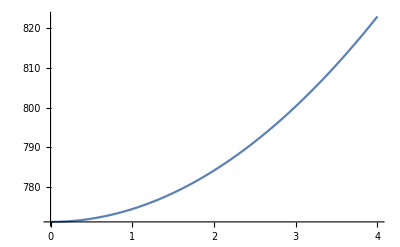

```mathematica
(*The expression for specific heat in the normal state*)
γ:=45.6 *10^-3*(5.75*10^3)/(340.0376*10^-3)(*J/(m^3*K^2) or 45.6 in mJ/mol/K^2*)
β:=10^-3*(5.75*10^3)/(340.0376*10^-3)*0.192(*{0,0.192}*)(*J/(m^3*K^4) or 0.192 in mJ/mol/K^4*) (*The allowed values are β={0,0.192}*)
CnbT[x_]:=γ+β*x^2(*Not if if the phonon contribution was subtracted form the original paper, if so then we should set β=0.*)
Plot[CnbT[x],{x,0,4}]
```

```mathematica
(*Testing the data that was recorder form the above graph for the normal state values*)
```

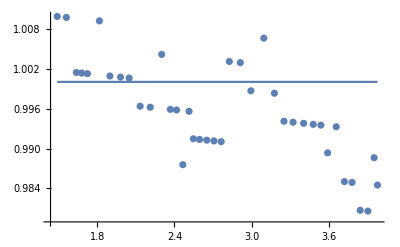

```mathematica
TvsCnbCn:={{3.9767225325884548,0.9845085308772459},{3.950651769087523,0.9886154310735316},{3.9022346368715084,0.9806054658009966},{3.8426443202979517,0.9807262569832402},{3.7793296089385473,0.9849086516684282},{3.7197392923649906,0.9850294428506718},{3.656424581005587,0.993265891589914},{3.589385474860335,0.989347727615884},{3.5372439478584727,0.9935074739544014},{3.477653631284916,0.993628265136645},{3.4031657355679705,0.9937792541144497},{3.32122905027933,0.9939453419900348},{3.250465549348231,0.9940887815189492},{3.1759776536312847,0.998293824550808},{3.094040968342645,1.0065680205345011},{2.9934823091247678,0.9986637475464293},{2.911545623836126,1.0028838894760683},{2.8258845437616387,1.0030575268005437},{2.7625698324022343,0.9910237052695154},{2.706703910614525,0.9911369470028688},{2.6508379888268156,0.9912501887362224},{2.594972067039106,0.9913634304695758},{2.5465549348230914,0.9914615733051488},{2.513035381750466,0.995583572399215},{2.4646182495344506,0.9875736071266799},{2.416201117318436,0.9957798580703612},{2.367783985102421,0.995878000905934},{2.300744878957169,1.0041219990940662},{2.211359404096834,0.9961950777593238},{2.133147113594041,0.9963536161860187},{2.047486033519553,1.0005813075645482},{1.9804469273743017,1.0007171976445723},{1.8985102420856612,1.0008832855201573},{1.8165735567970205,1.0091574815038504},{1.723463687150838,1.0012381096179983},{1.6787709497206704,1.0013287030046811},{1.6378026070763503,1.0014117469424735},{1.5595903165735567,1.0096783934772764},{1.488826815642458,1.0098218330061908}}
Tnbn=Range[Length[TvsCnbCn]];(*Just the temp in the normal state*)
fnbn=Range[Length[TvsCnbCn]];
For[i=1,i<=Length[TvsCnbCn],i++,Tnbn[[i]]=TvsCnbCn[[i]][[1]];fnbn[[i]]=TvsCnbCn[[i]][[2]]]
Length[Tnbn];
Tnbn;
fnbn;
plt1n1=ListPlot[Transpose@{Tnbn,fnbn}];(*Cp vs temp*)
plt1n2=Plot[{1},{x,Tnbn[[1]],Tnbn[[Length[Tnbn]]]}];
Show[plt1n1,plt1n2]
```

```mathematica
(*Data for <ϵ> = 0%*)
TvsCsbCn1:={{1.0083798882681565,1.197282198399517},{1.0232774674115457,1.2094141627661186},{1.041899441340782,1.2255926317378834},{1.0605214152700186,1.2498792088177566},{1.0754189944134078,1.2741733353465199},{1.0977653631284916,1.2984523629775029},{1.1201117318435754,1.3267854446625398},{1.1461824953445066,1.3591650309527408},{1.179702048417132,1.391529518345161},{1.1983240223463687,1.4320323116412503},{1.2430167597765363,1.4684282047410542},{1.2690875232774674,1.512969953193417},{1.2988826815642458,1.5453419900347276},{1.3510242085661082,1.585776838290805},{1.388268156424581,1.6181337762343353},{1.40316573556797,1.5897252000603959},{1.40316573556797,1.5370224973576931},{1.4180633147113595,1.4923977049675377},{1.4180633147113595,1.4478031103729427},{1.4217877094972067,1.382930696059188},{1.4292364990689013,1.2977804620262723},{1.4366852886405959,1.2166842820474109},{1.4441340782122905,1.1477502642307114},{1.4478584729981379,1.0990940661331725},{1.4553072625698324,1.0707005888570136},{1.462756052141527,1.0504152196889631},{1.4739292364990688,1.034176355126076},{1.4925512104283054,1.0098142835573005},{1.5186219739292364,1.013815491469123},{1.5595903165735567,1.0056243394232223},{1.600558659217877,1.0014872414313758},{1.6564245810055866,1.0054280537520763},{1.7011173184357542,1.0012834063113396},{1.7569832402234637,1.0011701645779862},{1.812849162011173,1.0010569228446327},{1.8687150837988828,1.0009436811112793},{1.9245810055865922,0.9967763853238716},{1.9692737430167597,1.0007398459912429},{2.0027932960893855,0.9966178468971767},{2.0512104283054002,0.9884115959534956},{2.0884543761638734,0.9923901555186474},{2.1405959031657353,0.9922844632341841},{2.1964618249534453,0.9921712215008307},{2.2523277467411544,0.9920579797674771},{2.304469273743017,0.991952287483014},{2.38268156424581,0.9917937490563191},{2.442271880819367,0.9957270119281294},{2.5018621973929234,0.9915521666918317},{2.56145251396648,0.98332326740148},{2.665735567970205,0.9831118828325534},{2.721601489757914,0.9789445870451459},{2.7960893854748603,0.9869017061754493},{2.8519553072625694,0.9948965725502039},{2.9189944134078214,0.9907066284161257},{2.9711359404096838,0.9865468820776084},{3.034450651769088,0.9904725955005285},{3.1350093109869652,1.0024309225426544},{3.2132216014897574,0.9982183300619056},{3.2690875232774674,0.989996980220444},{3.3361266294227185,0.993915144194474},{3.395716945996276,0.981632190850068},{3.455307262569833,0.9936735618299866},{3.5074487895716944,0.9895138154914691},{3.5521415270018624,0.9894232221047863},{3.615456238361266,0.9892948814736524},{3.67877094972067,0.9810584327344105},{3.7458100558659213,0.9809225426543864},{3.8202979515828677,0.9848256077306357},{3.8798882681564244,0.9806507624943379},{3.9432029795158288,0.9845764759172579},{3.9916201117318444,0.988532387135739}}
```

```mathematica
T1=Range[Length[TvsCsbCn1]];
f1=Range[Length[TvsCsbCn1]];
For[i=1,i<=Length[TvsCsbCn1],i++,T1[[i]]=TvsCsbCn1[[i]][[1]];f1[[i]]=TvsCsbCn1[[i]][[2]]]
{Length[T1],Length[f1]};
T1;
f1;
```

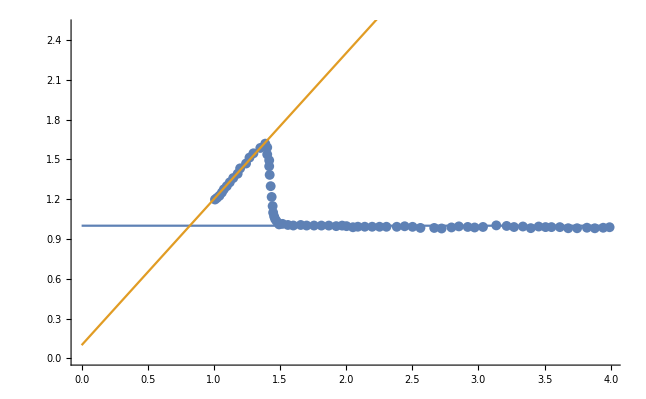

```mathematica
plt11=ListPlot[Transpose@{T1,f1}];(*Cp vs temp*)
plt12=Plot[{1,1.1x+0.1},{x,0,T1[[Length[T1]]]}];
Show[plt11,plt12,PlotRange->{0,2.5},AxesOrigin->Automatic](*{1.4,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0%*)
Δη[[1]]=0;
CpOnset[[1]]=1.5;
CpEnd[[1]]=1.4;
Tc[[1]]=(CpEnd[[1]]+CpOnset[[1]])/2;
m[[1]]=1.1;
c[[1]]=0.1;
y1=Range[Length[T1]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0%*)
For[i=1,i<=Length[y1],i++,y1[[i]]=(1-f1[[i]])*CnbT[T1[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T1[[i]]<=CpOnset[[1]],i++,Δη[[1]]+=(T1[[i+1]]-T1[[i]])*((y1[[i]]+y1[[i+1]])/2)](*The Discrete sum*)
Δη[[1]]
Δη[[1]]+=Integrate[(1-(m[[1]]x+c[[1]]))*CnbT[x],{x,0,T1[[1]]}](*c>0, thus first term*)
```

-143.867

124.768

-146.949

127.435

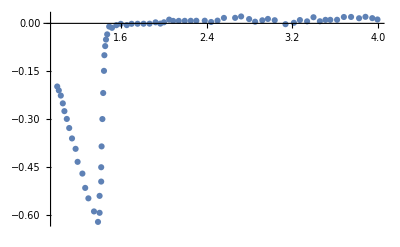

```mathematica
(*Sanity check for <ϵ> = 0%*)
((CpEnd[[1]]-T1[[1]])*(1-f1[[1]]+1-Max[f1])*γ)/2+((CpOnset[[1]]-CpEnd[[1]])*(1-Max[f1])*γ)/2(*To test second line of 1177, we use an estimate to test the numerical integral*)
(T1[[1]]-(1-c[[1]])/m[[1]])*γ/2*(1-f1[[1]])+((1-c[[1]])/m[[1]])*γ/2*(1-c[[1]])-142(*To test last line of 1177, we use an estimate to test*)
ListPlot[Transpose@{T1,y1/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.14%*)TvsCsbCn2:={{1.004655493482309,1.0797221802808399},{1.0195530726256983,1.1040163068096032},{1.0381750465549349,1.1242488298354223},{1.0567970204841712,1.1525894609693497},{1.0716945996275604,1.1728295334440588},{1.0865921787709496,1.189015551864714},{1.1052141527001862,1.2214102370526956},{1.12756052141527,1.2416352106296245},{1.1499068901303537,1.2659142382606072},{1.1685288640595903,1.2983089234485885},{1.1834264432029795,1.3144949418692438},{1.1983240223463687,1.338789068398007},{1.2132216014897579,1.3671372489808247},{1.2355679702048419,1.3954703306658616},{1.2616387337057728,1.4400120791182245},{1.2877094972067038,1.4561754491922092},{1.3063314711359404,1.4845160803261366},{1.324953445065177,1.5128567114600635},{1.3472998137802605,1.5371357390910467},{1.3696461824953445,1.5695228748301377},{1.410614525139665,1.5937641552166695},{1.4366852886405959,1.6180356333987622},{1.4664804469273742,1.6422995621319645},{1.4776536312849162,1.565249886758267},{1.4925512104283054,1.5084629322059493},{1.4925512104283054,1.4638683376113546},{1.5037243947858472,1.4151970406160352},{1.5037243947858472,1.3624943379133327},{1.5148975791433892,1.309768986863959},{1.522346368715084,1.252997131209422},{1.522346368715084,1.2002944285067192},{1.5335195530726258,1.159731239619508},{1.5409683426443204,1.1353918163974033},{1.5558659217877095,1.0867129699531937},{1.574487895716946,1.05424279027631},{1.5931098696461825,1.0298807187075345},{1.6266294227188083,1.0135965574513064},{1.675046554934823,1.0094443605616792},{1.7309124767225326,1.0052770647742717},{1.783054003724395,1.0011173184357545},{1.820297951582868,0.996987769892798}}
```

```mathematica
T2=Range[Length[TvsCsbCn2]];
f2=Range[Length[TvsCsbCn2]];
For[i=1,i<=Length[TvsCsbCn2],i++,T2[[i]]=TvsCsbCn2[[i]][[1]];f2[[i]]=TvsCsbCn2[[i]][[2]]]
{Length[T2],Length[f2]};
T2;
f2;
```

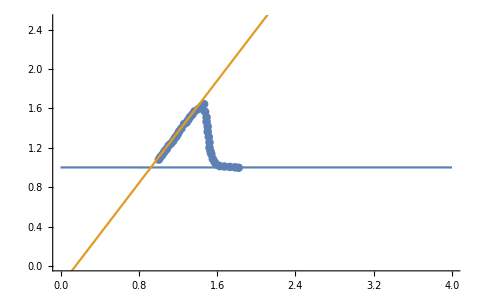

```mathematica
plt21=ListPlot[Transpose@{T2,f2}];(*Cp vs temp*)
plt22=Plot[{1,1.3x-0.2},{x,0,4}];
Show[plt21,plt22,PlotRange->{0,2.5},AxesOrigin->Automatic](*{1.48,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.14%*)
Δη[[2]]=0;
CpOnset[[2]]=1.6;
CpEnd[[2]]=1.48;
Tc[[2]]=(CpEnd[[2]]+CpOnset[[2]])/2;
m[[2]]=1.3;
c[[2]]=-0.2;
y2=Range[Length[T2]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.14%*)
For[i=1,i<=Length[y2],i++,y2[[i]]=(1-f2[[i]])*CnbT[T2[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T2[[i]]<=CpOnset[[2]],i++,Δη[[2]]+=(T2[[i+1]]-T2[[i]])*((y2[[i]]+y2[[i+1]])/2)](*The Discrete sum*)
Δη[[2]]+=Integrate[(1-(m[[2]]x+c[[2]]))*CnbT[x],{x,-c[[2]]/m[[2]],T2[[1]]}](*Second term for c<0*)
Δη[[2]]+=Integrate[CnbT[x],{x,0,-c[[2]]/m[[2]]}](*First term for c<0*)
```

129.919

248.553

247.573

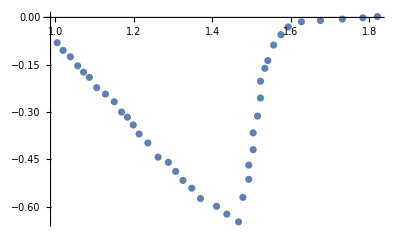

```mathematica
(*Sanity check for <ϵ> = 0.14%*)
γ*(1*(-c[[2]])/m[[2]]+1/2*((1-c[[2]])/m[[2]]+c[[2]]/m[[2]])*1+1/2*(CpOnset[[2]]-(1-c[[2]])/m[[2]])*(1-Max[f2]))(*Order of MAgnitude analysis to test the integral above*)
ListPlot[Transpose@{T2,y2/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.24%*)TvsCsbCn3:={{1.004655493482309,0.9135059640646235},{1.0270018621973929,0.9296768835874987},{1.0381750465549349,0.953978559565152},{1.0493482309124766,0.9701721274346975},{1.0716945996275604,0.9944511550656805},{1.090316573556797,1.0187377321455537},{1.116387337057728,1.0470632643817004},{1.1350093109869646,1.0754038955156278},{1.1573556797020483,1.1077910312547186},{1.179702048417132,1.152340329155972},{1.2057728119180633,1.1847199154461727},{1.2243947858472999,1.217114600634154},{1.2541899441340782,1.2373244753133024},{1.2802607076350092,1.2737581156575573},{1.2988826815642458,1.3102068548995924},{1.3286778398510242,1.3506869998490114},{1.3696461824953445,1.3951985505058133},{1.3845437616387337,1.423546731088631},{1.4068901303538173,1.4599879208817759},{1.4553072625698324,1.4963762645326892},{1.4739292364990688,1.5328250037747246},{1.5074487895716948,1.5854597614374155},{1.5595903165735567,1.6340027178016008},{1.5968342644320297,1.6582515476370228},{1.622905027932961,1.6784689717650614},{1.6415270018621975,1.6176204137097994},{1.6564245810055866,1.577049675373698},{1.6601489757914338,1.5081232070058888},{1.6675977653631284,1.4675675675675677},{1.6787709497206704,1.4391665408425187},{1.6787709497206704,1.3945719462479242},{1.6899441340782122,1.3459006492526049},{1.7011173184357542,1.264796919824853},{1.7085661080074488,1.2404574966027482},{1.712290502793296,1.2161256228295336},{1.7197392923649908,1.1634078212290506},{1.7271880819366852,1.1350143439528917},{1.73463687150838,1.1147289747848408},{1.7420856610800743,1.090389551562736},{1.7569832402234637,1.061980975388797},{1.783054003724395,1.0416578589762948},{1.809124767225326,1.0334969047259552},{1.8500931098696463,1.0131435905178925},{1.883612662942272,1.0171296995319343},{1.920856610800745,1.0048920428808699},{1.9767225325884543,1.0047788011475165},{2.0176908752327747,1.004695757209724},{2.06610800744879,1.0045976143741508},{2.10707635009311,1.0004605163823044},{2.1517690875232773,1.0003699229956216}}
```

```mathematica
T3=Range[Length[TvsCsbCn3]];
f3=Range[Length[TvsCsbCn3]];
For[i=1,i<=Length[TvsCsbCn3],i++,T3[[i]]=TvsCsbCn3[[i]][[1]];f3[[i]]=TvsCsbCn3[[i]][[2]]]
{Length[T3],Length[f3]};
T3;
f3;
```

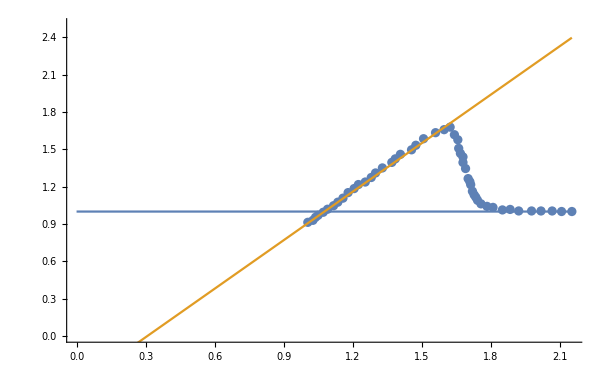

```mathematica
plt31=ListPlot[Transpose@{T3,f3}];(*Cp vs temp*)
plt32=Plot[{1,1.3x-0.4},{x,0,T3[[Length[T3]]]}];
Show[plt31,plt32,PlotRange->{0,2.5},AxesOrigin->Automatic](*{1.62,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.24%*)
Δη[[3]]=0;
CpOnset[[3]]=1.85;
CpEnd[[3]]=1.62;
Tc[[3]]=(CpEnd[[3]]+CpOnset[[3]])/2;
m[[3]]=1.3;
c[[3]]=-0.4;
y3=Range[Length[T3]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.24%*)
For[i=1,i<=Length[y3],i++,y3[[i]]=(1-f3[[i]])*CnbT[T3[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T3[[i]]<=CpOnset[[3]],i++,Δη[[3]]+=(T3[[i+1]]-T3[[i]])*((y3[[i]]+y3[[i+1]])/2)](*The Discrete sum*)
Δη[[3]]+=Integrate[(1-(m[[3]]x+c[[3]]))*CnbT[x],{x,-c[[3]]/m[[3]],T3[[1]]}](*Second term for c<0*)
Δη[[3]]+=Integrate[CnbT[x],{x,0,-c[[3]]/m[[3]]}](*First term for c<0*)
```

101.873

339.164

331.61

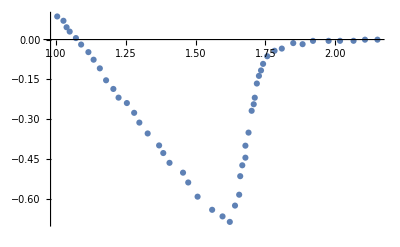

```mathematica
(*Sanity check for <ϵ> = 0.24%*)
γ*(1*(-c[[3]])/m[[3]]+1/2*((1-c[[3]])/m[[3]]+c[[3]]/m[[3]])*1+1/2*(CpOnset[[3]]-(1-c[[3]])/m[[3]])*(1-Max[f3]))(*Order of MAgnitude analysis to test the integral above*)
ListPlot[Transpose@{T3,y3/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.32%*)TvsCsbCn4:={{1.0083798882681565,0.7189038200211386},{1.0307262569832403,0.7350747395440136},{1.0456238361266292,0.755314812018723},{1.0679702048417132,0.779593839649706},{1.0865921787709496,0.811988524837687},{1.116387337057728,0.8281443454627813},{1.1424581005586592,0.8686320398610905},{1.1685288640595903,0.9010116261512913},{1.1871508379888267,0.9252982032311643},{1.2094972067039107,0.9536312849162014},{1.228119180633147,0.9819719160501286},{1.250465549348231,1.0103049977351657},{1.2802607076350092,1.0507851426845845},{1.3212290502793296,1.1034048014494944},{1.3547486033519553,1.1317152347878607},{1.391992551210428,1.1762343348935531},{1.4068901303538173,1.2086365695304246},{1.4366852886405959,1.2531707685338973},{1.4664804469273742,1.2733806432130457},{1.4962756052141526,1.3179148422165186},{1.522346368715084,1.3584025366148273},{1.5521415270018621,1.4029367356183},{1.585661080074488,1.4434093311188285},{1.6340782122905029,1.4879057828778501},{1.6713221601489758,1.5364789370375966},{1.712290502793296,1.5809904876943985},{1.7383612662942272,1.6255322361467615},{1.7793296089385475,1.6578816246414014},{1.835195530726257,1.6820927072323724},{1.8873370577281192,1.6536086365695306},{1.9022346368715084,1.5927676279631588},{1.920856610800745,1.4954325834214104},{1.9320297951582868,1.4467612864260908},{1.9432029795158285,1.40619809753888},{1.9506517690875234,1.3575343499924508},{1.9655493482309125,1.2966933413860788},{1.9655493482309125,1.2602068548995924},{1.9804469273743017,1.211528008455383},{1.9916201117318435,1.1750188736222258},{2.01024208566108,1.1384946398912883},{2.032588454376164,1.10196285671146},{2.058659217877095,1.0654235240827423},{2.0847299813780262,1.0451004076702404},{2.1145251396648046,1.0328778499169562},{2.155493482309125,1.0165785897629473},{2.200186219739292,1.0083798882681567},{2.2411545623836124,1.00424279027631},{2.293296089385475,1.0041370979918467},{2.34171322160149,1.0040389551562738},{2.3975791433891995,1.0039257134229203},{2.47951582867784,1.003759625547335},{2.542830540037244,0.9995772308621473},{2.6210428305400373,0.9953646383813983},{2.6918063314711356,0.995221198852484},{2.7588454376163876,0.9950853087724598},{2.7960893854748603,0.9950098142835575},{2.889199255121043,0.9988751321153557},{2.922718808193668,0.9988071870753437}}
```

```mathematica
T4=Range[Length[TvsCsbCn4]];
f4=Range[Length[TvsCsbCn4]];
For[i=1,i<=Length[TvsCsbCn4],i++,T4[[i]]=TvsCsbCn4[[i]][[1]];f4[[i]]=TvsCsbCn4[[i]][[2]]]
{Length[T4],Length[f4]};
T4;
f4;
```

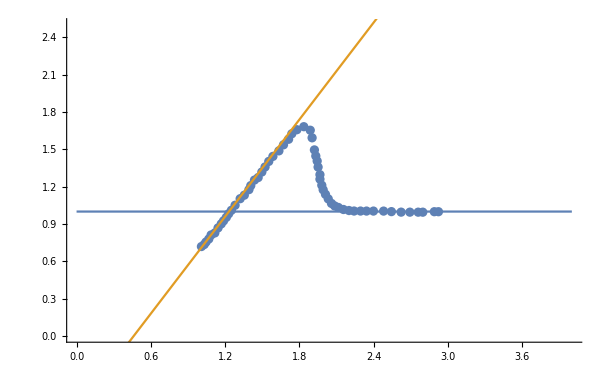

```mathematica
plt41=ListPlot[Transpose@{T4,f4}];(*Cp vs temp*)
plt42=Plot[{1,1.3x-0.6},{x,0,4}];
Show[plt41,plt42,PlotRange->{0,2.5},AxesOrigin->Automatic](*{1.88,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.32%*)
Δη[[4]]=0;
CpOnset[[4]]=2.2;
CpEnd[[4]]=1.88;
Tc[[4]]=(CpEnd[[4]]+CpOnset[[4]])/2;
m[[4]]=1.3;
c[[4]]=-0.6;
y4=Range[Length[T4]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.32%*)
For[i=1,i<=Length[y4],i++,y4[[i]]=(1-f4[[i]])*CnbT[T4[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T4[[i]]<=CpOnset[[4]],i++,Δη[[4]]+=(T4[[i+1]]-T4[[i]])*((y4[[i]]+y4[[i+1]])/2)](*The Discrete sum*)
Δη[[4]]+=Integrate[(1-(m[[4]]x+c[[4]]))*CnbT[x],{x,-c[[4]]/m[[4]],T4[[1]]}](*Second term for c<0*)
Δη[[4]]+=Integrate[CnbT[x],{x,0,-c[[4]]/m[[4]]}](*First term for c<0*)
```

58.8378

414.832

397.576

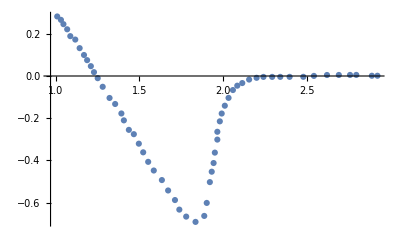

```mathematica
(*Sanity check for <ϵ> = 0.32%*)
γ*(1*(-c[[4]])/m[[4]]+1/2*((1-c[[4]])/m[[4]]+c[[4]]/m[[4]])*1+1/2*(CpOnset[[4]]-(1-c[[4]])/m[[4]])*(1-Max[f4]))
ListPlot[Transpose@{T4,y4/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.39%*)TvsCsbCn5:={{1.0083798882681565,0.5486335497508685},{1.0232774674115457,0.5567114600634155},{1.0381750465549349,0.5688434244300171},{1.053072625698324,0.5850294428506724},{1.0679702048417132,0.5971614072172735},{1.0828677839851024,0.6133474256379288},{1.1052141527001862,0.6335723992148579},{1.1201117318435754,0.645704363581459},{1.1350093109869646,0.6659444360561682},{1.1573556797020483,0.6821153555790429},{1.1685288640595903,0.6983089234485884},{1.1834264432029795,0.7144949418692439},{1.1983240223463687,0.734735014343953},{1.2132216014897579,0.7549750868186627},{1.2355679702048419,0.7711460063415372},{1.2616387337057728,0.791363430469576},{1.2690875232774674,0.8156726558961198},{1.2877094972067038,0.8277970708138307},{1.3100558659217878,0.8480220443907598},{1.324953445065177,0.8723161709195231},{1.3435754189944134,0.892548693945342},{1.3696461824953445,0.924928280235543},{1.3547486033519553,0.9087422618148879},{1.3845437616387337,0.9411142986561987},{1.40316573556797,0.9532387135739093},{1.4180633147113595,0.9775328401026726},{1.4329608938547487,0.9977729125773822},{1.4441340782122905,1.0058583723388195},{1.4590316573556796,1.0179903367054208},{1.4702048417132216,1.0382379586290202},{1.488826815642458,1.0665785897629476},{1.5186219739292364,1.0989506266042581},{1.5409683426443204,1.1272837082892952},{1.5633147113594041,1.1556167899743321},{1.574487895716946,1.1799184659519857},{1.6042830540037243,1.2001283406311343},{1.6378026070763503,1.2324928280235543},{1.6527001862197395,1.264895062660426},{1.686219739292365,1.2932054959987924},{1.7197392923649908,1.3255699833912127},{1.7458100558659218,1.3741657858976295},{1.7793296089385475,1.40653027329005},{1.8054003724394785,1.4348558055261968},{1.8314711359404097,1.4753434999245059},{1.861266294227188,1.5077155367658164},{1.8947858472998138,1.5400800241582369},{1.9245810055865922,1.5805601691076552},{1.946927374301676,1.5845689264683682},{1.9729981378026071,1.5966782424882986},{1.9916201117318435,1.6250188736222257},{2.0363128491620115,1.6492526045598672},{2.0623836126629422,1.665415974633852},{2.0884543761638734,1.6694171825456743},{2.1145251396648046,1.7017967688358753},{2.1517690875232773,1.726045598671297},{2.1815642458100557,1.697606824701797},{2.200186219739292,1.6610825909708593},{2.2150837988826817,1.6205118526347577},{2.218808193668529,1.5799637626453271},{2.2374301675977653,1.5474935829684435},{2.2411545623836124,1.5069454929790127},{2.2523277467411544,1.4582741959836933},{2.259776536312849,1.4339347727615885},{2.270949720670391,1.3974256379284316},{2.2783985102420856,1.3609240525441646},{2.2970204841713224,1.3000754944889024},{2.304469273743017,1.2716820172127437},{2.315642458100559,1.2351728823795864},{2.3379888268156424,1.1905329910916504},{2.356610800744879,1.1580628114147669},{2.3752327746741155,1.1255926317378833},{2.393854748603352,1.1012305601691077},{2.4236499068901303,1.0849539483617698},{2.442271880819367,1.052483768684886},{2.47951582867784,1.0361920579797674},{2.5242085661080074,1.0198852483768688},{2.5689013035381754,1.011686546882078},{2.6210428305400373,1.0075268005435605},{2.662011173184357,1.0033897025517138},{2.706703910614525,0.9951910010569229},{2.743947858472998,0.9951155065680206},{2.7849162011173183,0.9950324626302283},{2.822160148975791,0.9990110221953801},{2.8594040968342647,0.9989355277064778}}
```

```mathematica
T5=Range[Length[TvsCsbCn5]];
f5=Range[Length[TvsCsbCn5]];
For[i=1,i<=Length[TvsCsbCn5],i++,T5[[i]]=TvsCsbCn5[[i]][[1]];f5[[i]]=TvsCsbCn5[[i]][[2]]]
{Length[T5],Length[f5]};
T5;
f5;
```

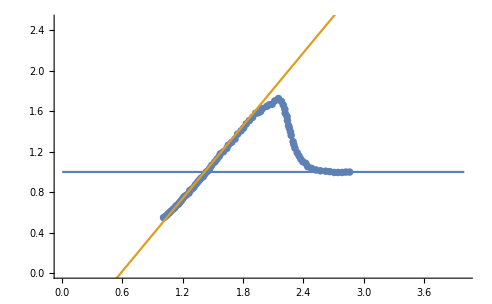

```mathematica
plt51=ListPlot[Transpose@{T5,f5}];(*Cp vs temp*)
plt52=Plot[{1,1.2x-0.7},{x,0,4}];(*This is different from the 1.3 slope and 0.8 intercept that was expected based on the pattern above*)
Show[plt51,plt52,PlotRange->{0,2.5},AxesOrigin->Automatic](*{2.16,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.39%*)
Δη[[5]]=0;
CpOnset[[5]]=2.5;
CpEnd[[5]]=2.16;
Tc[[5]]=(CpEnd[[5]]+CpOnset[[5]])/2;
m[[5]]=1.2;
c[[5]]=-0.7;
y5=Range[Length[T5]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.39%*)
For[i=1,i<=Length[y5],i++,y5[[i]]=(1-f5[[i]])*CnbT[T5[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T5[[i]]<=CpOnset[[5]],i++,Δη[[5]]+=(T5[[i+1]]-T5[[i]])*((y5[[i]]+y5[[i+1]])/2)](*The Discrete sum*)
Δη[[5]]+=Integrate[(1-(m[[5]]x+c[[5]]))*CnbT[x],{x,-c[[5]]/m[[5]],T5[[1]]}](*Second term for c<0*)
Δη[[5]]+=Integrate[CnbT[x],{x,0,-c[[5]]/m[[5]]}](*First term for c<0*)
```

14.8697

464.888

467.841

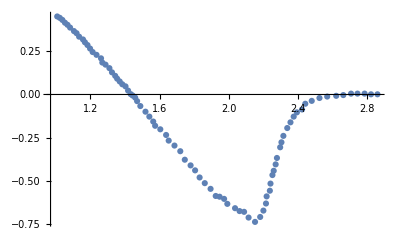

```mathematica
(*Sanity check for <ϵ> = 0.39%*)
γ*(1*(-c[[5]])/m[[5]]+1/2*((1-c[[5]])/m[[5]]+c[[5]]/m[[5]])*1+1/2*(CpOnset[[5]]-(1-c[[5]])/m[[5]])*(1-Max[f5]))
ListPlot[Transpose@{T5,y5/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.44%*)TvsCsbCn6:={{1.0083798882681565,0.42701192812924704},{1.0307262569832403,0.43912879359806745},{1.0567970204841712,0.4593462177261065},{1.0865921787709496,0.47955609240525443},{1.116387337057728,0.499765967084403},{1.138733705772812,0.5199909406613321},{1.1610800744878957,0.548324022346369},{1.1945996275605213,0.5766344556847351},{1.216945996275605,0.5928053752076103},{1.2355679702048419,0.6170919522874831},{1.2728119180633146,0.6453948361769595},{1.3063314711359404,0.6858674316774875},{1.3435754189944134,0.7141703155669639},{1.391992551210428,0.7546127132719316},{1.4217877094972067,0.7950928582213501},{1.4739292364990688,0.8598520308017517},{1.522346368715084,0.904348482560773},{1.574487895716946,0.9569454929790129},{1.608007448789572,0.9974180884795414},{1.648975791433892,1.0378755850822892},{1.6787709497206704,1.074301675977654},{1.723463687150838,1.1106975690774576},{1.7569832402234637,1.1673863807942022},{1.8054003724394785,1.20782877849917},{1.835195530726257,1.2442548693945343},{1.87243947858473,1.2847199154461728},{1.9245810055865922,1.333262871810358},{1.9581005586592177,1.3777895213649405},{1.9916201117318435,1.4142080628114149},{2.0400372439478582,1.4546504605163824},{2.0772811918063314,1.5032236146761289},{2.118249534450652,1.5517892193869849},{2.155493482309125,1.5760380492224069},{2.1927374301675977,1.6286652574362073},{2.2523277467411544,1.6488147365242338},{2.300744878957169,1.6811490261210933},{2.345437616387337,1.7337611354371132},{2.3975791433891995,1.7458176053148122},{2.4646182495344506,1.745681715234788},{2.4869646182495346,1.7496904725955007},{2.509310986964618,1.7009965272535106},{2.52048417132216,1.6685414464744075},{2.542830540037244,1.6441718254567417},{2.56145251396648,1.595485429563642},{2.5689013035381754,1.5387135739091047},{2.580074487895717,1.4981503850218933},{2.594972067039106,1.449471538577684},{2.602420856610801,1.396753736977201},{2.6098696461824953,1.37646836780915},{2.61731843575419,1.3561829986410994},{2.632216014897579,1.32777442246716},{2.6359404096834265,1.3034425486939454},{2.654562383612663,1.2831345311792242},{2.665735567970205,1.2587875585082289},{2.6731843575418996,1.2141778650158541},{2.688081936685289,1.1817152347878606},{2.706703910614525,1.1776234334893552},{2.732774674115457,1.1573003170768534},{2.7513966480446923,1.1369922995621322},{2.777467411545624,1.112615129095576},{2.8072625698324023,1.0882304091801298},{2.8407821229050283,1.0638381398157937},{2.8817504655493478,1.0434848256077307},{2.9264432029795158,1.0231239619507775},{2.967411545623836,1.0108787558508232},{3.0083798882681565,1.0148497659670845},{3.060521415270019,1.0147440736826212},{3.116387337057728,1.010576777895214},{3.172253258845438,1.0104635361618604},{3.228119180633147,1.010350294428507},{3.276536312849162,0.9940359353767176},{3.317504655493482,1.002060999547033},{3.4068901303538173,1.0018798127736677},{3.4925512104283056,0.9976521213951384}}
```

```mathematica
T6=Range[Length[TvsCsbCn6]];
f6=Range[Length[TvsCsbCn6]];
For[i=1,i<=Length[TvsCsbCn6],i++,T6[[i]]=TvsCsbCn6[[i]][[1]];f6[[i]]=TvsCsbCn6[[i]][[2]]]
{Length[T6],Length[f6]};
T6;
f6;
```

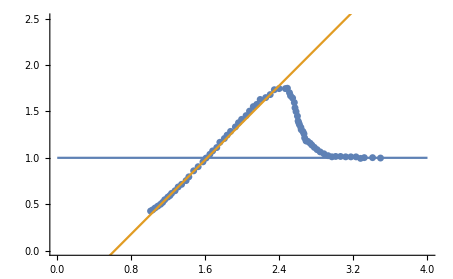

```mathematica
plt61=ListPlot[Transpose@{T6,f6}];(*Cp vs temp*)
plt62=Plot[{1,1*x-0.62},{x,0,4}];(*the slope is 1 and the intercept is -0.62!! breaking the trend*)
Show[plt61,plt62,PlotRange->{0,2.5},AxesOrigin->Automatic](*{2.9,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.44%*)
Δη[[6]]=0;
CpOnset[[6]]=2.9;
CpEnd[[6]]=2.5;
Tc[[6]]=(CpEnd[[6]]+CpOnset[[6]])/2;
m[[6]]=1;
c[[6]]=-0.62;
y6=Range[Length[T6]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.44%*)
For[i=1,i<=Length[y6],i++,y6[[i]]=(1-f6[[i]])*CnbT[T6[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T6[[i]]<=CpOnset[[6]],i++,Δη[[6]]+=(T6[[i+1]]-T6[[i]])*((y6[[i]]+y6[[i+1]])/2)](*The Discrete sum*)
Δη[[6]]+=Integrate[(1-(m[[6]]x+c[[6]]))*CnbT[x],{x,-c[[6]]/m[[6]],T6[[1]]}](*Second term for c<0*)
Δη[[6]]+=Integrate[CnbT[x],{x,0,-c[[6]]/m[[6]]}](*First term for c<0*)
```

-14.152

464.182

493.651

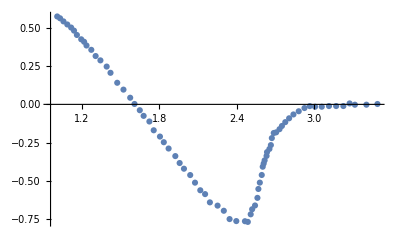

```mathematica
(*Sanity check for <ϵ> = 0.44%*)
γ*(1*(-c[[6]])/m[[6]]+1/2*((1-c[[6]])/m[[6]]+c[[6]]/m[[6]])*1+1/2*(CpOnset[[6]]-(1-c[[6]])/m[[6]])*(1-Max[f6]))
ListPlot[Transpose@{T6,y6/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.48%*)TvsCsbCn7:={{1.0083798882681565,0.34998490110222},{1.0307262569832403,0.3580477125169863},{1.053072625698324,0.3701645779858076},{1.079143389199255,0.3863279480597921},{1.1052141527001862,0.4065453721878307},{1.1350093109869646,0.4227011928129252},{1.1610800744878957,0.43886456288690967},{1.175977653631285,0.46315868941567295},{1.1983240223463687,0.4793296089385475},{1.2243947858472999,0.4954929790125324},{1.250465549348231,0.5197644571946252},{1.2728119180633146,0.5399894307715538},{1.2951582867783986,0.5561603502944286},{1.3212290502793296,0.5723237203684135},{1.3435754189944134,0.5925486939453424},{1.3659217877094973,0.6168277215763251},{1.3957169459962757,0.645145704363582},{1.4292364990689013,0.669402083647894},{1.4478584729981379,0.693688660727767},{1.4702048417132216,0.7098595802506422},{1.4962756052141526,0.7341310584327347},{1.5186219739292364,0.7543560320096636},{1.5446927374301676,0.7826815642458103},{1.5670391061452513,0.8069605918767933},{1.5931098696461825,0.831232070058886},{1.622905027932961,0.8554959987920885},{1.6452513966480447,0.8716669183149632},{1.6638733705772812,0.8918994413407821},{1.686219739292365,0.9161784689717656},{1.7085661080074488,0.9323493884946401},{1.7420856610800743,0.9647138758870604},{1.760707635009311,0.9930545070209877},{1.7793296089385475,1.0173410841008608},{1.812849162011173,1.041597463385173},{1.835195530726257,1.0699305450702101},{1.8538175046554934,1.0982711762041373},{1.8761638733705772,1.114442095727012},{1.8985102420856612,1.1265589611958329},{1.9059590316573556,1.154922240676431},{1.9320297951582868,1.1751396648044694},{1.9618249534450651,1.1912954854295639},{1.9767225325884543,1.2236977200664354},{1.9990689013035383,1.235814585535256},{2.021415270018622,1.2641476672202931},{2.047486033519553,1.29247319945644},{2.0698324022346366,1.3086441189793145},{2.0959031657355682,1.3288615431073534},{2.121973929236499,1.3531330212894461},{2.144320297951583,1.381466102974483},{2.1703910614525137,1.4016835271025216},{2.200186219739292,1.4218934017816702},{2.222532588454376,1.4461724294126528},{2.24487895716946,1.4663974029895819},{2.267225325884544,1.4947304846746188},{2.293296089385475,1.5149479088026574},{2.3119180633147116,1.5432885399365848},{2.3379888268156424,1.5472897478484073},{2.3640595903165735,1.5634531179223918},{2.38268156424581,1.5715234787860486},{2.393854748603352,1.6039332628718104},{2.408752327746741,1.6282273894005739},{2.4385474860335195,1.6443832100256683},{2.4646182495344506,1.6564925260455987},{2.483240223463687,1.6726709950173637},{2.509310986964618,1.6888343650913484},{2.5353817504655494,1.692835573003171},{2.5540037243947857,1.71306809602899},{2.5726256983240225,1.7292465650007551},{2.606145251396648,1.7535029442850671},{2.6359404096834265,1.7656047108561075},{2.665735567970205,1.7898686395893102},{2.710428305400373,1.7857239921485732},{2.75512104283054,1.7694171825456744},{2.7849162011173183,1.745032462630228},{2.8035381750465547,1.7247244451155066},{2.8184357541899443,1.6598293824550807},{2.8296089385474863,1.6192661935678696},{2.8370577281191807,1.5746565000754944},{2.8482309124767227,1.5584176355126078},{2.8594040968342647,1.546232825003775},{2.8631284916201123,1.5300090593386684},{2.866852886405959,1.5097312396195077},{2.8705772811918067,1.4894534199003475},{2.878026070763501,1.4732221047863507},{2.8854748603351954,1.4529367356182998},{2.889199255121043,1.4326589158991394},{2.8966480446927374,1.4164276007851428},{2.900372439478585,1.4002038351200363},{2.9078212290502794,1.3718103578438774},{2.9152700186219738,1.3515249886758267},{2.9264432029795158,1.3271780160048317},{2.9413407821229054,1.3028234938849463},{2.956238361266294,1.2825230258191154},{2.956238361266294,1.2581987014947908},{2.9711359404096838,1.2338441793749058},{2.98975791433892,1.2135361618601843},{3.004655493482309,1.1932356937943531},{3.015828677839851,1.1729427751774122},{3.027001862197393,1.144541748452363},{3.0530726256983236,1.1363807942020234},{3.0679702048417132,1.1282424882983542},{3.082867783985102,1.1241582364487395},{3.0903165735567972,1.1079269213347427},{3.1089385474860336,1.0916729578740751},{3.1350093109869643,1.0835120036237356},{3.149906890130354,1.0591574815038505},{3.1871508379888267,1.0590819870149482},{3.2020484171322163,1.0387815189491167},{3.2355679702048414,1.0265514117469425},{3.2914338919925514,1.026438170013589},{3.317504655493482,1.0142231617091952},{3.343575418994413,1.0020081534048015},{3.3696461824953445,0.9979012532085159},{3.410614525139665,1.0059263173788315},{3.4627560521415273,0.9896044088781519},{3.4962756052141524,0.9895364638381399},{3.5297951582867784,0.9894685187981278},{3.555865921787709,0.9975237807640045},{3.5856610800744884,0.9893552770647742},{3.615456238361266,0.9892948814736524}}
```

```mathematica
T7=Range[Length[TvsCsbCn7]];
f7=Range[Length[TvsCsbCn7]];
For[i=1,i<=Length[TvsCsbCn7],i++,T7[[i]]=TvsCsbCn7[[i]][[1]];f7[[i]]=TvsCsbCn7[[i]][[2]]]
{Length[T7],Length[C7]};
T7;
f7;
```

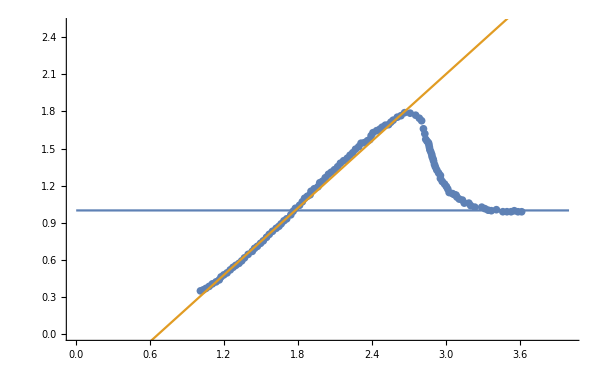

```mathematica
plt71=ListPlot[Transpose@{T7,f7}];(*Cp vs temp*)
plt72=Plot[{1,0.9x-0.6},{x,0,4}];
Show[plt71,plt72,PlotRange->{0,2.5},AxesOrigin->Automatic](*{2.73,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.48%*)
Δη[[7]]=0;
CpOnset[[7]]=3.25;
CpEnd[[7]]=2.73;
Tc[[7]]=(CpEnd[[7]]+CpOnset[[7]])/2;
m[[7]]=0.9;
c[[7]]=-0.6;
y7=Range[Length[T7]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.48%*)
For[i=1,i<=Length[y7],i++,y7[[i]]=(1-f7[[i]])*CnbT[T7[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T7[[i]]<=CpOnset[[7]],i++,Δη[[7]]+=(T7[[i+1]]-T7[[i]])*((y7[[i]]+y7[[i+1]])/2)](*The Discrete sum*)
Δη[[7]]+=Integrate[(1-(m[[7]]x+c[[7]]))*CnbT[x],{x,-c[[7]]/m[[7]],T7[[1]]}](*Second term for c<0*)
Δη[[7]]+=Integrate[CnbT[x],{x,0,-c[[7]]/m[[7]]}](*First term for c<0*)
```

-41.0418

473.34

494.108

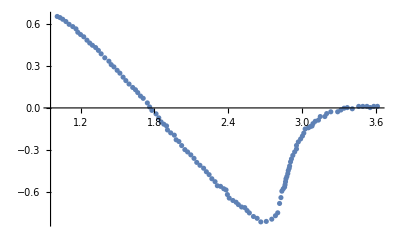

```mathematica
(*Sanity check for <ϵ> = 0.48%*)
γ*(1*(-c[[7]])/m[[7]]+1/2*((1-c[[7]])/m[[7]]+c[[7]]/m[[7]])*1+1/2*(CpOnset[[7]]-(1-c[[7]])/m[[7]])*(1-Max[f7]))
ListPlot[Transpose@{T7,y7/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.50%*)TvsCsbCn8:={{1.0069767441860464,0.307432432432432},{1.0330232558139534,0.3195945945945944},{1.0627906976744186,0.33581081081081043},{1.0925581395348836,0.35202702702702693},{1.1186046511627907,0.368243243243243},{1.1372093023255814,0.38445945945945903},{1.1669767441860464,0.4006756756756755},{1.1967441860465116,0.4249999999999998},{1.233953488372093,0.4493243243243241},{1.267441860465116,0.47364864864864864},{1.2972093023255813,0.5020270270270268},{1.3381395348837208,0.5304054054054053},{1.371627906976744,0.5506756756756757},{1.3939534883720928,0.575},{1.4348837209302325,0.6033783783783784},{1.4720930232558138,0.6398648648648648},{1.5093023255813953,0.676351351351351},{1.5390697674418603,0.6966216216216214},{1.5651162790697675,0.7209459459459457},{1.583720930232558,0.7412162162162159},{1.613488372093023,0.7695945945945946},{1.632093023255814,0.7939189189189189},{1.661860465116279,0.8182432432432429},{1.6841860465116278,0.8344594594594594},{1.7251162790697672,0.866891891891892},{1.7548837209302324,0.89527027027027},{1.773488372093023,0.9236486486486486},{1.7995348837209302,0.9398648648648646},{1.8181395348837208,0.9641891891891889},{1.851627906976744,0.9925675675675674},{1.8851162790697673,1.0209459459459458},{1.9148837209302325,1.0574324324324322},{1.9409302325581392,1.0817567567567568},{1.9595348837209299,1.110135135135135},{1.989302325581395,1.1304054054054054},{2.011627906976744,1.1547297297297296},{2.030232558139535,1.179054054054054},{2.063720930232558,1.2114864864864865},{2.089767441860465,1.2277027027027028},{2.11953488372093,1.2520270270270268},{2.1530232558139533,1.2804054054054053},{2.171627906976744,1.3128378378378378},{2.193953488372093,1.341216216216216},{2.2274418604651163,1.3695945945945946},{2.253488372093023,1.3898648648648648},{2.27953488372093,1.410135135135135},{2.3130232558139534,1.4344594594594593},{2.335348837209302,1.4668918918918918},{2.361395348837209,1.487162162162162},{2.383720930232558,1.5155405405405404},{2.413488372093023,1.5439189189189189},{2.43953488372093,1.5763513513513512},{2.4804651162790696,1.6087837837837835},{2.506511627906977,1.6290540540540541},{2.5399999999999996,1.6614864864864864},{2.5846511627906974,1.6614864864864864},{2.6032558139534885,1.702027027027027},{2.629302325581395,1.7222972972972972},{2.651627906976744,1.7385135135135135},{2.6665116279069765,1.7466216216216215},{2.692558139534883,1.7709459459459458},{2.729767441860465,1.775},{2.7520930232558136,1.8033783783783783},{2.7967441860465114,1.8358108108108109},{2.837674418604651,1.843918918918919},{2.8748837209302325,1.839864864864865},{2.9195348837209303,1.8479729729729728},{2.949302325581395,1.8277027027027026},{2.990232558139535,1.8114864864864866},{3.0125581395348835,1.7709459459459458},{3.023720930232558,1.7506756756756756},{3.027441860465116,1.7263513513513513},{3.0386046511627907,1.697972972972973},{3.0460465116279067,1.6736486486486486},{3.0572093023255813,1.6614864864864864},{3.064651162790698,1.625},{3.072093023255814,1.5844594594594594},{3.07953488372093,1.552027027027027},{3.0906976744186045,1.5074324324324324},{3.098139534883721,1.487162162162162},{3.1130232558139532,1.4506756756756756},{3.124186046511628,1.4304054054054054},{3.131627906976744,1.3979729729729728},{3.1353488372093024,1.3655405405405405},{3.146511627906977,1.3533783783783784},{3.161395348837209,1.337162162162162},{3.1651162790697676,1.3128378378378378},{3.1799999999999997,1.2844594594594594},{3.202325581395349,1.2601351351351349},{3.213488372093023,1.2317567567567567},{3.2320930232558136,1.2074324324324324},{3.2506976744186047,1.191216216216216},{3.2693023255813953,1.1668918918918918},{3.284186046511628,1.1466216216216216},{3.3027906976744186,1.1304054054054054},{3.3288372093023253,1.110135135135135},{3.343720930232558,1.093918918918919},{3.366046511627907,1.0898648648648648},{3.3920930232558137,1.0736486486486485},{3.4069767441860463,1.04527027027027},{3.433023255813953,1.0533783783783783},{3.4590697674418602,1.0290540540540538},{3.4962790697674415,1.025},{3.526046511627907,1.0128378378378378},{3.55953488372093,1.0128378378378378},{3.585581395348837,1.0047297297297297},{3.622790697674419,1.0006756756756756},{3.630232558139535,1.0047297297297297},{3.6637209302325577,1.0047297297297297},{3.689767441860465,1.0087837837837836},{3.7195348837209297,1.0047297297297297},{3.7604651162790694,1.0047297297297297},{3.790232558139535,0.9966216216216215},{3.8237209302325583,1.0087837837837836},{3.8609302325581396,1.0087837837837836},{3.913023255813953,1.0128378378378378},{3.9502325581395348,1.0006756756756756}}
```

```mathematica
T8=Range[Length[TvsCsbCn8]];
f8=Range[Length[TvsCsbCn8]];
For[i=1,i<=Length[TvsCsbCn8],i++,T8[[i]]=TvsCsbCn8[[i]][[1]];f8[[i]]=TvsCsbCn8[[i]][[2]]]
{Length[T8],Length[f8]};
T8;
f8;
```

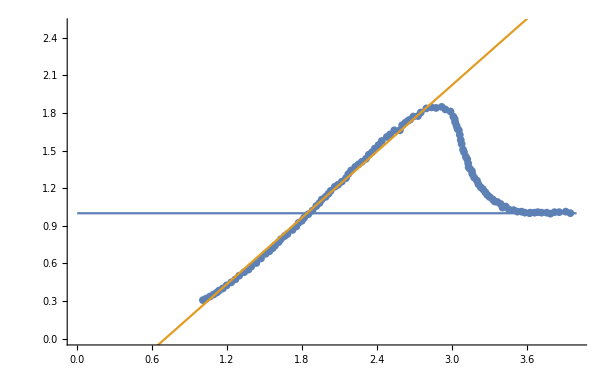

```mathematica
plt81=ListPlot[Transpose@{T8,f8}];(*Cp vs temp*)
plt82=Plot[{1,0.88x-0.62},{x,0,4}];
Show[plt81,plt82,PlotRange->{0,2.5},AxesOrigin->Automatic]
```

```mathematica
(*Storing Values for <ϵ> = 0.50%*)
Δη[[8]]=0;
CpOnset[[8]]=3.5;
CpEnd[[8]]=2.935;
Tc[[8]]=(CpEnd[[8]]+CpOnset[[8]])/2;
m[[8]]=0.9;
c[[8]]=-0.6;
y8=Range[Length[T8]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.50%*)
For[i=1,i<=Length[y8],i++,y8[[i]]=(1-f8[[i]])*CnbT[T8[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T8[[i]]<=CpOnset[[8]],i++,Δη[[8]]+=(T8[[i+1]]-T8[[i]])*((y8[[i]]+y8[[i+1]])/2)](*The Discrete sum*)
Δη[[8]]+=Integrate[(1-(m[[8]]x+c[[8]]))*CnbT[x],{x,-c[[8]]/m[[8]],T8[[1]]}](*Second term for c<0*)
Δη[[8]]+=Integrate[CnbT[x],{x,0,-c[[8]]/m[[8]]}](*First term for c<0*)
```

-102.388

411.993

379.395

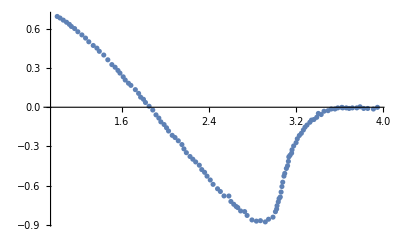

```mathematica
(*Sanity check for <ϵ> = 0.50%*)
γ*(1*(-c[[8]])/m[[8]]+1/2*((1-c[[8]])/m[[8]]+c[[8]]/m[[8]])*1+1/2*(CpOnset[[8]]-(1-c[[8]])/m[[8]])*(1-Max[f8]))
ListPlot[Transpose@{T8,y8/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.53%*)TvsCsbCn9:={{1.0069767441860464,0.2709459459459458},{1.0330232558139534,0.2831081081081077},{1.0553488372093023,0.29121621621621596},{1.073953488372093,0.30337837837837833},{1.0925581395348836,0.31554054054054026},{1.1186046511627907,0.33175675675675675},{1.1446511627906977,0.3439189189189187},{1.1632558139534883,0.3641891891891893},{1.181860465116279,0.3763513513513512},{1.2041860465116279,0.38445945945945903},{1.2265116279069765,0.4006756756756755},{1.2451162790697674,0.4168918918918916},{1.267441860465116,0.42905405405405395},{1.2972093023255813,0.4412162162162163},{1.3158139534883722,0.45743243243243215},{1.3306976744186045,0.47364864864864864},{1.3530232558139534,0.49391891891891904},{1.371627906976744,0.5020270270270268},{1.4013953488372093,0.522297297297297},{1.423720930232558,0.5466216216216213},{1.4460465116279069,0.570945945945946},{1.4683720930232558,0.583108108108108},{1.4869767441860464,0.6033783783783784},{1.5093023255813953,0.6155405405405405},{1.5241860465116277,0.6317567567567566},{1.5427906976744183,0.6479729729729728},{1.5651162790697675,0.660135135135135},{1.58,0.6844594594594593},{1.6023255813953488,0.7006756756756753},{1.6172093023255814,0.7128378378378379},{1.63953488372093,0.729054054054054},{1.6655813953488372,0.7452702702702703},{1.6953488372093022,0.7736486486486485},{1.7213953488372091,0.7979729729729728},{1.7548837209302324,0.8182432432432429},{1.7809302325581395,0.8506756756756755},{1.8032558139534882,0.883108108108108},{1.8330232558139534,0.9033783783783782},{1.8665116279069767,0.9317567567567568},{1.8962790697674419,0.9682432432432431},{1.926046511627907,0.9966216216216215},{1.9595348837209299,1.0209459459459458},{2.0004651162790696,1.0614864864864864},{2.0227906976744183,1.0858108108108109},{2.0488372093023255,1.114189189189189},{2.074883720930232,1.1385135135135134},{2.1046511627906974,1.162837837837838},{2.1232558139534885,1.187162162162162},{2.1493023255813952,1.2195945945945945},{2.1865116279069765,1.247972972972973},{2.2125581395348832,1.2763513513513511},{2.2348837209302324,1.3087837837837837},{2.260930232558139,1.337162162162162},{2.2906976744186043,1.3695945945945946},{2.3204651162790695,1.3898648648648648},{2.353953488372093,1.410135135135135},{2.3725581395348834,1.4263513513513513},{2.387441860465116,1.4628378378378377},{2.420930232558139,1.483108108108108},{2.454418604651163,1.5074324324324324},{2.4841860465116277,1.5317567567567565},{2.521395348837209,1.5682432432432432},{2.5586046511627907,1.5966216216216216},{2.6069767441860465,1.6290540540540541},{2.6367441860465113,1.6614864864864864},{2.673953488372093,1.697972972972973},{2.7111627906976743,1.7344594594594596},{2.7520930232558136,1.7668918918918919},{2.7930232558139534,1.79527027027027},{2.833953488372093,1.8155405405405405},{2.8748837209302325,1.8601351351351352},{2.9232558139534883,1.8682432432432432},{2.975348837209302,1.8966216216216214},{3.016279069767442,1.9452702702702702},{3.094418604651163,1.9736486486486486},{3.161395348837209,1.9452702702702702},{3.1874418604651162,1.9006756756756755},{3.2283720930232556,1.8844594594594595},{3.243255813953488,1.852027027027027},{3.2506976744186047,1.7668918918918919},{3.261860465116279,1.7466216216216215},{3.2693023255813953,1.714189189189189},{3.2730232558139534,1.685810810810811},{3.287906976744186,1.6371621621621621},{3.2953488372093025,1.6128378378378376},{3.3027906976744186,1.5925675675675675},{3.3065116279069766,1.5682432432432432},{3.317674418604651,1.5236486486486487},{3.3325581395348833,1.4993243243243242},{3.34,1.4466216216216217},{3.3623255813953485,1.3939189189189187},{3.373488372093023,1.3736486486486486},{3.3846511627906977,1.3452702702702701},{3.3920930232558137,1.325},{3.3995348837209303,1.3087837837837837},{3.4106976744186044,1.2763513513513511},{3.414418604651163,1.256081081081081},{3.433023255813953,1.2277027027027028},{3.447906976744186,1.2114864864864865},{3.4590697674418602,1.191216216216216},{3.4702325581395352,1.162837837837838},{3.485116279069767,1.1466216216216216},{3.492558139534884,1.1304054054054054},{3.5,1.1060810810810808},{3.51860465116279,1.0898648648648648},{3.548372093023256,1.0655405405405405},{3.574418604651163,1.041216216216216},{3.593023255813953,1.025},{3.622790697674419,1.0047297297297297},{3.6562790697674417,1.0006756756756756},{3.682325581395349,0.9966216216216215},{3.723255813953488,0.9966216216216215},{3.7865116279069766,1.0006756756756756},{3.8311627906976744,0.9966216216216215},{3.8795348837209302,1.0047297297297297},{3.9502325581395348,1.0047297297297297}}
```

```mathematica
T9=Range[Length[TvsCsbCn9]];
f9=Range[Length[TvsCsbCn9]];
For[i=1,i<=Length[TvsCsbCn9],i++,T9[[i]]=TvsCsbCn9[[i]][[1]];f9[[i]]=TvsCsbCn9[[i]][[2]]]
{Length[T9],Length[f9]};
T9;
f9;
```

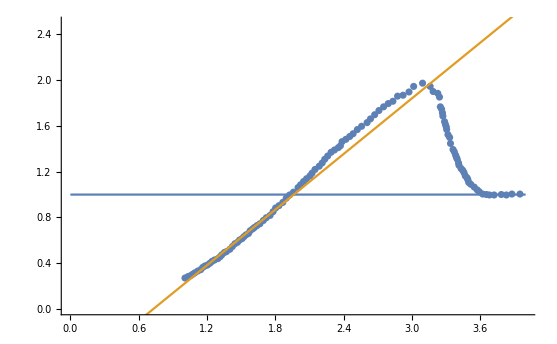

```mathematica
plt91=ListPlot[Transpose@{T9,f9}];(*Cp vs temp*)
plt92=Plot[{1,0.81x-0.59},{x,0,4}];
Show[plt91,plt92,PlotRange->{0,2.5},AxesOrigin->Automatic](*{3.1,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.53%*)
Δη[[9]]=0;
CpOnset[[9]]=3.6;
CpEnd[[9]]=3.1;
Tc[[9]]=(CpEnd[[9]]+CpOnset[[9]])/2;
m[[9]]=0.81;
c[[9]]=-0.59;
y9=Range[Length[T9]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.53%*)
For[i=1,i<=Length[y9],i++,y9[[i]]=(1-f9[[i]])*CnbT[T9[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T9[[i]]<=CpOnset[[9]],i++,Δη[[9]]+=(T9[[i+1]]-T9[[i]])*((y9[[i]]+y9[[i+1]])/2)](*The Discrete sum*)
Δη[[9]]+=Integrate[(1-(m[[9]]x+c[[9]]))*CnbT[x],{x,-c[[9]]/m[[9]],T9[[1]]}](*Second term for c<0*)
Δη[[9]]+=Integrate[CnbT[x],{x,0,-c[[9]]/m[[9]]}](*First term for c<0*)
```

-216.756

345.321

423.121

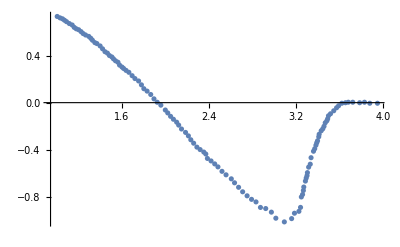

```mathematica
(*Sanity check for <ϵ> = 0.53%*)
γ*(1*(-c[[9]])/m[[9]]+1/2*((1-c[[9]])/m[[9]]+c[[9]]/m[[9]])*1+1/2*(CpOnset[[9]]-(1-c[[9]])/m[[9]])*(1-Max[f9]))
ListPlot[Transpose@{T9,y9/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

```mathematica
(*Data for <ϵ> = 0.57%*)TvsCsbCn10:={{1.0106976744186047,0.26283783783783754},{1.0293023255813953,0.26689189189189166},{1.044186046511628,0.27905405405405403},{1.0627906976744186,0.29121621621621596},{1.0851162790697675,0.30337837837837833},{1.1074418604651162,0.3114864864864866},{1.1260465116279068,0.3236486486486485},{1.1446511627906977,0.33581081081081043},{1.1669767441860464,0.3479729729729728},{1.1855813953488372,0.3641891891891893},{1.2004651162790698,0.3763513513513512},{1.2190697674418605,0.3885135135135136},{1.233953488372093,0.3966216216216214},{1.2451162790697674,0.40878378378378377},{1.263720930232558,0.4168918918918916},{1.2823255813953487,0.42905405405405395},{1.2972093023255813,0.4412162162162163},{1.3158139534883722,0.45337837837837824},{1.3344186046511628,0.4695945945945943},{1.3567441860465115,0.47770270270270254},{1.3790697674418604,0.49797297297297294},{1.3939534883720928,0.5101351351351351},{1.4125581395348834,0.522297297297297},{1.4348837209302325,0.5385135135135135},{1.4534883720930232,0.5587837837837835},{1.4758139534883719,0.570945945945946},{1.4981395348837208,0.5952702702702701},{1.5130232558139534,0.6074324324324323},{1.5316279069767442,0.6236486486486483},{1.553953488372093,0.6398648648648648},{1.5725581395348835,0.660135135135135},{1.5874418604651162,0.6722972972972971},{1.609767441860465,0.6966216216216214},{1.6283720930232555,0.7168918918918918},{1.6469767441860463,0.7209459459459457},{1.661860465116279,0.7412162162162159},{1.6879069767441859,0.7655405405405402},{1.710232558139535,0.789864864864865},{1.7399999999999998,0.814189189189189},{1.769767441860465,0.8385135135135133},{1.7958139534883721,0.8628378378378376},{1.8218604651162789,0.891216216216216},{1.855348837209302,0.9236486486486486},{1.8888372093023253,0.960135135135135},{1.9223255813953486,0.9844594594594593},{1.9483720930232558,1.0128378378378378},{1.985581395348837,1.0533783783783783},{2.0079069767441857,1.0777027027027026},{2.0451162790697675,1.118243243243243},{2.0786046511627907,1.1466216216216216},{2.115813953488372,1.1749999999999998},{2.145581395348837,1.2033783783783782},{2.1790697674418604,1.247972972972973},{2.201395348837209,1.2682432432432431},{2.2162790697674417,1.2885135135135135},{2.2348837209302324,1.3168918918918917},{2.253488372093023,1.341216216216216},{2.283255813953488,1.3574324324324323},{2.309302325581395,1.3898648648648648},{2.3502325581395347,1.410135135135135},{2.3725581395348834,1.4304054054054054},{2.391162790697674,1.4587837837837836},{2.4246511627906977,1.4952702702702703},{2.4432558139534883,1.5236486486486487},{2.469302325581395,1.5439189189189189},{2.4879069767441857,1.564189189189189},{2.510232558139535,1.564189189189189},{2.5288372093023255,1.5925675675675675},{2.551162790697674,1.6128378378378376},{2.569767441860465,1.6290540540540541},{2.5846511627906974,1.6533783783783784},{2.6181395348837206,1.6655405405405403},{2.6367441860465113,1.685810810810811},{2.6590697674418604,1.714189189189189},{2.6665116279069765,1.7304054054054054},{2.692558139534883,1.7668918918918919},{2.7074418604651163,1.787162162162162},{2.7334883720930234,1.7912162162162162},{2.7483720930232556,1.8033783783783783},{2.7744186046511627,1.8236486486486485},{2.781860465116279,1.856081081081081},{2.811627906976744,1.8682432432432432},{2.8302325581395347,1.8925675675675675},{2.8488372093023253,1.9047297297297296},{2.8786046511627905,1.912837837837838},{2.886046511627907,1.9412162162162163},{2.9306976744186044,1.9777027027027025},{2.9567441860465116,1.997972972972973},{3.001395348837209,2.022297297297297},{3.0348837209302326,2.0385135135135135},{3.0572093023255813,2.0547297297297296},{3.0869767441860465,2.079054054054054},{3.1204651162790698,2.1074324324324323},{3.1427906976744184,2.1195945945945946},{3.157674418604651,2.139864864864865},{3.1725581395348836,2.152027027027027},{3.198604651162791,2.1804054054054056},{3.2283720930232556,2.200675675675676},{3.2581395348837208,2.2128378378378377},{3.287906976744186,2.229054054054054},{3.3325581395348833,2.2452702702702703},{3.366046511627907,2.2493243243243244},{3.418139534883721,2.237162162162162},{3.4441860465116276,2.1966216216216217},{3.4665116279069768,2.160135135135135},{3.485116279069767,2.1358108108108107},{3.507441860465116,2.087162162162162},{3.5223255813953487,2.0425675675675676},{3.526046511627907,1.997972972972973},{3.5372093023255813,1.9371621621621622},{3.5409302325581398,1.8885135135135136},{3.548372093023256,1.8358108108108109},{3.555813953488372,1.7831081081081082},{3.5632558139534884,1.7344594594594596},{3.566976744186046,1.6533783783783784},{3.574418604651163,1.5277027027027028},{3.581860465116279,1.3898648648648648},{3.581860465116279,1.2722972972972972},{3.593023255813953,1.1831081081081078},{3.5967441860465117,1.110135135135135},{3.6004651162790697,1.0533783783783783},{3.6116279069767443,1.033108108108108},{3.6265116279069765,1.0006756756756756},{3.6711627906976747,0.9966216216216215},{3.715813953488372,1.0006756756756756},{3.764186046511628,1.0006756756756756},{3.8051162790697672,1.0087837837837836},{3.8423255813953485,0.9925675675675674},{3.872093023255814,0.9844594594594593},{3.909302325581395,0.9925675675675674},{3.9539534883720933,0.9925675675675674},{3.987441860465116,0.9925675675675674}}
```

```mathematica
T10=Range[Length[TvsCsbCn10]];
f10=Range[Length[TvsCsbCn10]];
For[i=1,i<=Length[TvsCsbCn10],i++,T10[[i]]=TvsCsbCn10[[i]][[1]];f10[[i]]=TvsCsbCn10[[i]][[2]]]
{Length[T10],Length[f10]};
T10;
f10;
```

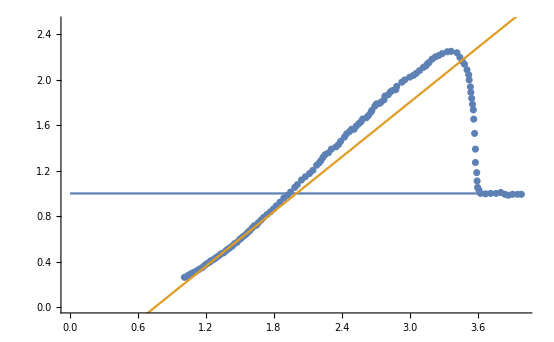

```mathematica
plt101=ListPlot[Transpose@{T10,f10}];(*Cp vs temp*)
plt102=Plot[{1,0.8x-0.6},{x,0,4}];
Show[plt101,plt102,PlotRange->{0,2.5},AxesOrigin->Automatic](*{3.40,1}*)
```

```mathematica
(*Storing Values for <ϵ> = 0.57%*)
Δη[[10]]=0;
CpOnset[[10]]=3.62;
CpEnd[[10]]=3.4;
Tc[[10]]=(CpEnd[[10]]+CpOnset[[10]])/2;
m[[10]]=0.8;
c[[10]]=-0.6;
y10=Range[Length[T10]];
```

```mathematica
(*Here we Calculate the area under the curve Subscript[C, n]/θ*[1-f(θ)] for <ϵ> = 0.57%*)
For[i=1,i<=Length[y10],i++,y10[[i]]=(1-f10[[i]])*CnbT[T10[[i]]]](*storing the integrand as values of y, just like stated above.*)
For[i=1,T10[[i]]<=CpOnset[[10]],i++,Δη[[10]]+=(T10[[i+1]]-T10[[i]])*((y10[[i]]+y10[[i+1]])/2)](*The Discrete sum*)
Δη[[10]]+=Integrate[(1-(m[[10]]x+c[[10]]))*CnbT[x],{x,-c[[10]]/m[[10]],T10[[1]]}](*Second term for c<0*)
Δη[[10]]+=Integrate[CnbT[x],{x,0,-c[[10]]/m[[10]]}](*First term for c<0*)
```

-505.904

72.8712

279.943

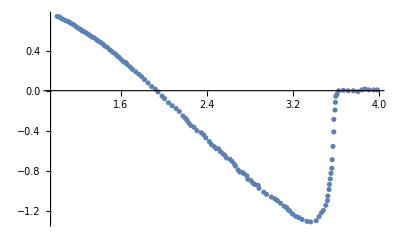

```mathematica
(*Sanity check for <ϵ> = 0.57%*)
γ*(1*(-c[[10]])/m[[10]]+1/2*((1-c[[10]])/m[[10]]+c[[10]]/m[[10]])*1+1/2*(CpOnset[[10]]-(1-c[[10]])/m[[10]])*(1-Max[f10]))
ListPlot[Transpose@{T10,y10/γ}](*We plot this as a means of Sanity check to see if the trend is respected.*)
```

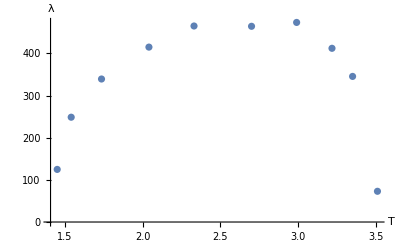

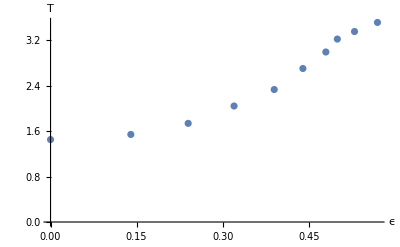

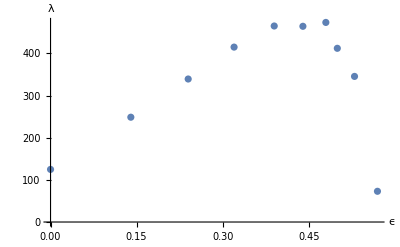

{124.768,248.553,339.164,414.832,464.888,464.182,473.34,411.993,345.321,72.8712}

```mathematica
(*Tc vs Δη and <ϵ>vs Δη*)
ListPlot[Transpose@{Tc,Δη},AxesLabel->{T,λ}](*HEre λ:=Δη*)
ListPlot[Transpose@{AvgEps,Tc},AxesLabel->{ϵ,T}]
ListPlot[Transpose@{AvgEps,Δη},AxesLabel->{ϵ,λ}]
Δη
```

```mathematica
(*Clausius Clayperon Equation*)
```

```mathematica
(*We can use the claussius clayperon relation to obtain dσ/Subscript[dθ, c]*(Subscript[ϵ, s]-Subscript[ϵ, n])=Subscript[η, n](Subscript[θ, c])-Subscript[η, s](Subscript[θ, c]), where the RHS is what we have computed above. We use the fact that the largest possible strian should be 0.6% while the lost is the zero strain case. Using the data reported in "Split superconducting and time-reversal symmetry-breaking transitions in Sr2RuO4 under stress", the change in Transition temperature with stress is given as Δσ/Subscript[Δθ, c]~1.25*10^6 
*)
```

```mathematica
Subscript[Δσ, c]=0.25+0.03125;(*Computing values from the curve*)
Δθ=0.125*9/5; (*Approximating from discrete curve*)
Subscript[Δσ, c]/Δθ
```

1.25

```mathematica
Subscript[Δσ, c]/Δθ*10^6*(0.57)/100(*The LHS of the Claussius Clayperon eqn.*)
```

7125.

```mathematica
450*Δθ/Subscript[Δσ, c]*10^-6*100 (*The ans is in percent, ie, of the clac give 4, then the ans is 4%.*)
```

0.036

```mathematica
(*The answer is saying that 1 strain is at 0.03% while the other is at 0%. This would never give an average strain of the order of 0.57% as we expect.*)
```

InterpolatingFunction[…]

InterpolatingFunction[…][x]

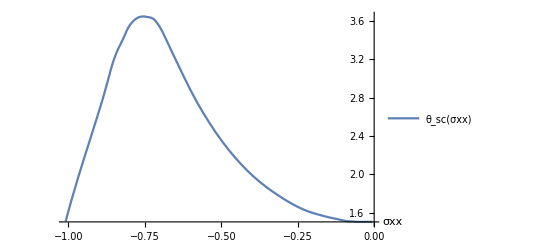

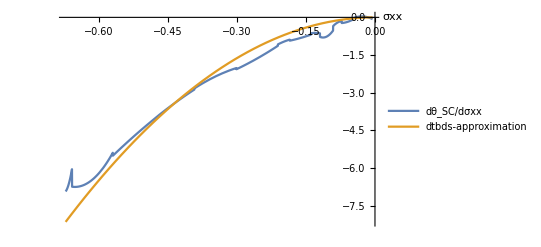

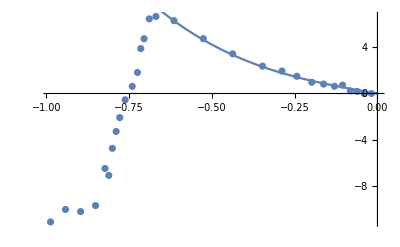

```mathematica
(*We extract data from the plot of Stress vs Transition Temperature 
-Graphics-
*)
σvsTc:={{-0.005244338498212375,1.5038230597971527},{-0.030989272943981128,1.5037331054489842},{-0.04958283671036967,1.5036681384197519},{-0.07246722288438634,1.5077810511165581},{-0.09106078665077488,1.511908956204726},{-0.11966626936829572,1.5327733675159858},{-0.1396901072705603,1.5452820193751666},{-0.18545887961859364,1.5828579495905823},{-0.2112038140643624,1.6079252279468168},{-0.2755661501787844,1.7041364007766058},{-0.30131108462455314,1.7543609118372423},{-0.3928486293206199,1.972070424259688},{-0.4815256257449346,2.277840246075117},{-0.5702026221692492,2.7010104871777574},{-0.6588796185935638,3.2625455081546115},{-0.6789034564958284,3.396647451418405},{-0.698927294398093,3.5265565225647983},{-0.7103694874851014,3.5810238803807066},{-0.7189511323003577,3.6145368725371876},{-0.730393325387366,3.6354612534138924},{-0.7504171632896306,3.647969905273074},{-0.7733015494636473,3.635311329500279},{-0.7833134684147796,3.614311986666767},{-0.7947556615017879,3.576536157899866},{-0.8061978545887962,3.5219888406633633},{-0.8162097735399285,3.4506750324210462},{-0.8290822407628129,3.366772612898954},{-0.8734207389749702,2.9347518634293097},{-0.9191895113230035,2.4649902674392745},{-0.9649582836710369,2.0036144156840403},{-1.0092967818831942,1.5087005844533903}}
Tcσ=Range[Length[σvsTc]];
σ=Range[Length[σvsTc]];
For[i=1,i<=Length[σvsTc],i++,Tcσ[[i]]=σvsTc[[i]][[2]];σ[[i]]=σvsTc[[i]][[1]]]
{Length[Tcσ],Length[σ]};
Tcσ;
σ;
θc=Interpolation[σvsTc](*Gives me θ_c(σ)*)
dTbds[x_]=D[θc[x],x](*Stands for Subscript[dθ, c]/dσ*)
Plot[{θc[x]},{x,σ[[Length[σ]]],σ[[1]]},AxesLabel->{ σxx},PlotLegends->{Subscript[θ, sc][σxx]}]
Plot[{dTbds[x],-18*x^2},{x,σ[[Length[σ]]]/1.5,σ[[1]]},AxesLabel->{ σxx},PlotLegends->{Subscript[dθ, SC]/dσxx,"dtbds-approximation"}]
dtbds=Range[Length[σ]-1];  (*dθ/dσ*)
σstar=Range[Length[σ]-1];(*θ^* corresponding to the y coordinate of the point which has the same slope as the discrete slope calculated above.*)
For[i=1,i<=Length[σ]-1,i++,dtbds[[i]]=(Tcσ[[i+1]]-Tcσ[[i]])/(σ[[i+1]]-σ[[i]]);σstar[[i]]=(σ[[i+1]]+σ[[i]])/2]
pltσ1=ListPlot[Transpose@{σ,Tcσ},AxesLabel->Automatic];(*Transition temp vs strain*)
Show[pltσ1,Plot[{1.5-6*(x-0.0)^3},{x,0,σ[[Length[σ]]]}]];
pltσ2 =ListPlot[Transpose@{σstar,-dtbds},AxesLabel->Automatic];(*Transition temp Subscript[θ, c] vs Subscript[dθ, c]/dσ. We have also changed the compression to tension by plotting -Subscript[dθ, c]/dσ = Subscript[dθ, c]/d(-σ). It also makes it easier to see.*)
pltσ2a = Plot[{5*Abs[x]+14*Abs[x]^3},{x,σstar[[Length[σstar]]],0}];
Show[pltσ2,pltσ2a]
```

-0.750417

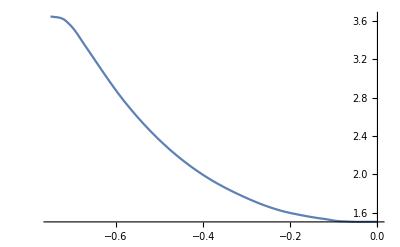

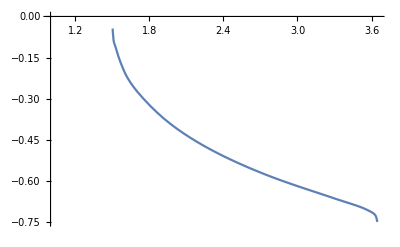

```mathematica
(*Creating the inverse function σ(Subscript[θ, SC])*)
σmax=σ[[Position[Tcσ,Max[Tcσ]][[1]][[1]]]]
θcR[x_]:=Piecewise[{{0,x<σmax},{θc[x],σmax<x<0}}];
Plot[θcR[x],{x,σmax,0}]
Subscript[σ, c][x_]:=InverseFunction[θcR][x]
Plot[Subscript[σ, c][x],{x,1,Max[Tcσ]}]
```

```mathematica
(*LHS/RHS*)
(*Theory
We have made measurements of the effect of stress on Transition temperature. From the above analysis, we have
Subscript[dθ, c]/dσ~=13.5*σ^1.6 i n units of K/MPa.
with σ \in (σmax,0)~(-0.7504171632896306,0)
Thus plugging this into the Claussius-Clayperon equation, we get
dσ/Subscript[dθ, c](Subscript[ϵ, 2]-Subscript[ϵ, 1])=Δη => 10^6/(13.5*σ^1.6)(Subscript[ϵ, 2]-Subscript[ϵ, 1])=Δη => 10^6/(13.5*σ^1.6)*57*10^-4=Δη => 422.22/σ^1.6=Δη
where we have used the fact that (Subscript[ϵ, 2]-Subscript[ϵ, 1])~0.57%, and in substituting the expression for dσ/Subscript[dθ, c], we converted the units to Pa/K, hence the 10^6.
We define a ratio to simplify the above
Ratio1=(dσ/Subscript[dθ, c](Subscript[ϵ, 2]-Subscript[ϵ, 1]))/Δη=422.22/(σ^1.6*Δη)
Alternatively, one can use the Claussius Clayperon equaton to get an expression for Subscript[ϵ, 2]-Subscript[ϵ, 1]=Subscript[ϵ, 2] (Assuming Subscript[ϵ, 1]~=0),
 Subscript[ϵ, 2]=100(Subscript[ϵ, 1]+Δη Subscript[dθ, c]/dσ) in %.
Subscript[ϵ, 2]=100*Δη*13.5/10^6*σ^1.6 where the units are in percentage
Alternatively, we can assume that <ϵ> = Subscript[ϵ, 2] and compute the Ratio 
Ratio2=(dσ/Subscript[dθ, c](Subscript[ϵ, 2]-Subscript[ϵ, 1]))/Δη=(10^6/(13.5*σ^1.6)*(<ϵ>)/100 )/Δη=(10^4/(13.5*σ^1.6)*<ϵ> )/Δη
*)
Tc
Δη
AvgEps
{Length[Δη],Length[Tc],Length[AvgEps]}
Ratio1=Range[Length[Δη]];
Ratio2=Range[Length[Δη]];
Eps=Range[Length[Δη]];
For[i=2,i<=Length[Δη],i++,s=Subscript[σ, c][Tc[[i]]];Ratio1[[i]]=422.22/Abs[s]^1.6*1/Δη[[i]]]
For[i=2,i<=Length[Δη],i++,s=Subscript[σ, c][Tc[[i]]];Eps[[i]]=Δη[[i]]*13.5/10^4*Abs[s]^1.6]
For[i=2,i<=Length[Δη],i++,s=Subscript[σ, c][Tc[[i]]];Ratio2[[i]]=10^4/13.5 AvgEps[[i]]/Abs[s]^1.6*1/Δη[[i]]]
Ratio1
Ratio2
Eps
```

{1.45,1.54,1.735,2.04,2.33,2.7,2.99,3.2175,3.35,3.51}

{124.768,248.553,339.164,414.832,464.888,464.182,473.34,411.993,345.321,72.8712}

{0,0.14,0.24,0.32,0.39,0.44,0.48,0.5,0.53,0.57}

{10,10,10}

{1,43.7738,8.93544,4.15074,2.80646,2.23577,1.92595,2.03062,2.30837,10.3453}

{1,10.7515,3.76231,2.33025,1.92022,1.72587,1.62186,1.78126,2.14639,10.3454}

{1,0.0130214,0.0637906,0.137324,0.203102,0.254945,0.295957,0.280701,0.246926,0.0550971}